```mathematica
randomi1 = RandomInteger[{1,2^2}]
randomi2 = RandomInteger[{1,2^3}]
randomi3 = RandomInteger[{1,2^2}]
randomi4 = RandomInteger[{1,2^3}]
randomk = RandomInteger[{1,2^3}]
```

2

4

4

4

«1 more identical outputs»

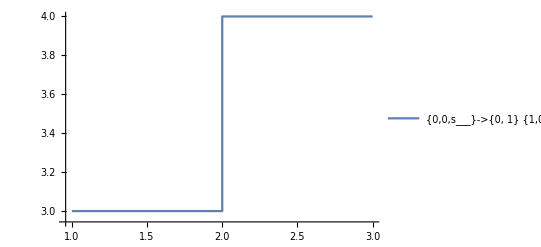
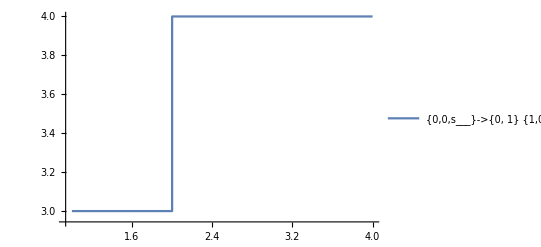
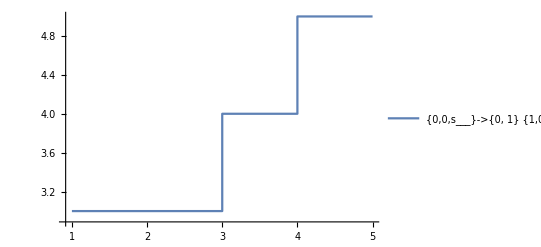
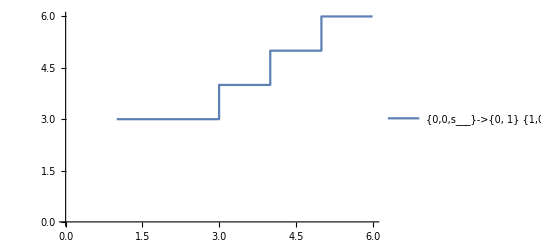
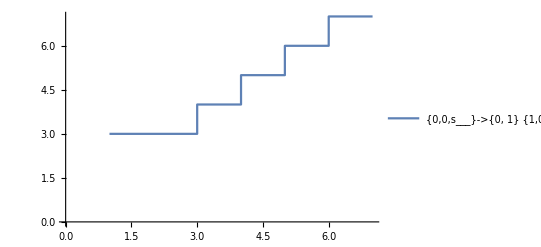
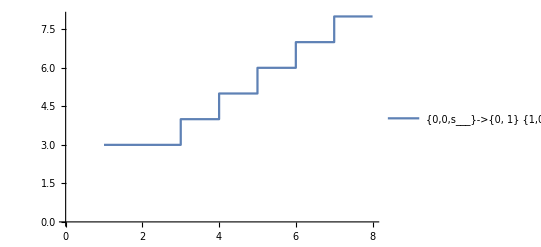
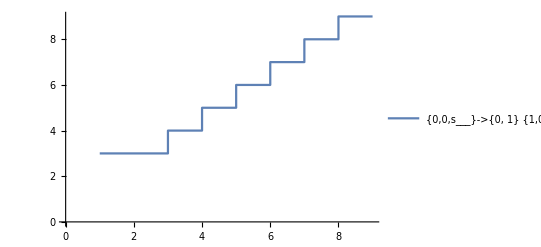
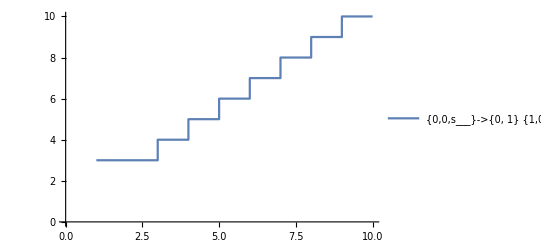

```mathematica
AllPathCanyonsBinary[g_]:=Style[Text[
With[
{
vertices=VertexList[g]
(*,randomInit=Tuples[{0,1},2]*)
},
Length /@FindShortestPath[g,First[VertexList[g]],vertices[[Length[vertices]]]]
]//.{x_}:>x]]

lFn[i1_,i2_,i3_,i4_,j_,k_,l_,t_]:= AllPathCanyonsBinary[
NestGraph[
ReplaceList[{
{left___,0,0,s___}:>Flatten[{left,s,0,1}],
{left___,1,0,s___}:>Flatten[{left,s,0,1,0}],
{left___,0,1,s___}:>Flatten[{left,s,1,0}],
{left___,1,1,s___}:>Flatten[{left,s,0,0,0}]

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[randomi4]]}]*)

(*{left___,0,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i1]]}],
{left___,1,0,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i2]]}],
{left___,0,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i3]]}],
{left___,1,1,s___}:>Flatten[{left,s,Tuples[{0,1},j][[i4]]}]*)
}],
{{0,1,1}},
(*{Tuples[{0,1},l][[randomk]]},*)
(*{Tuples[{0,1},l][[k]]},*)
t,
VertexShapeFunction->_->(Inset[ArrayPlot[{#2},ImageSize->32],#1,#3]&),
GraphLayout->"LayeredDigraphEmbedding",
PerformanceGoal->"Quality"
]]

Table[Table[Table[Table[Table[Show[
ListStepPlot[
Legended[
lFn[i1,i2,i3,i4,j,k,l,t][[1]][[1]],
StringTemplate[
"{0,0,s___}->`a`
{1,0,s___}->`b`
{0,1,s___}->`c`
{1,1,s___}->`d`
`e`"]
[<|
"a"->{0,1},
"b"->{0,1,0},
"c":>{1,0},
"d":>{0,0,0},
"e":>{0,1,1}


(*"a"->Tuples[{0,1},j][[randomi1]],
"b"->Tuples[{0,1},j][[randomi2]],
"c":>Tuples[{0,1},j][[randomi3]],
"d":>Tuples[{0,1},j][[randomi4]],
"e":>Tuples[{0,1},l][[randomk]]*)


(*"a"->Tuples[{0,1},j][[i1]],
"b"->Tuples[{0,1},j][[i2]],
"c":>Tuples[{0,1},j][[i3]],
"d":>Tuples[{0,1},j][[i4]],
"e":>Tuples[{0,1},l][[k]]*)
|>]
]]],{t,1,10}],
{i1,2^j,2^j},
{i2,2^j,2^j},
{i3,2^j,2^j},
{i4,2^j,2^j}],
{j,3,3}],
{k,2^l,2^l}],
{l,3,3}]/.{{{{{{{{x_}}}}}}}} -> x
```